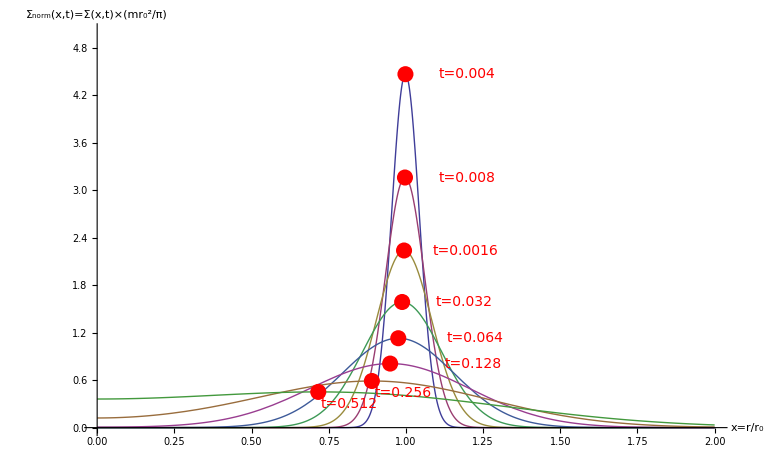

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:densityEvolutionDiffusion
* Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Plot the soloution of a PDE varing a parameter. 
   * Invocation: none
*)
t1=0.004;
t2=0.008;
t3=0.016;
t4=0.032;
t5=0.064;
t6=0.128;
t7=0.256;
t8 = 0.512;
S1[x_,t1_]=(1/t1)x^(-1/4)Exp[-(1+x^2)/t1]*BesselI[1/4,(2x)/t1];
S2[x_,t2_]=(1/t2)x^(-1/4)Exp[-(1+x^2)/t2]*BesselI[1/4,(2x)/t2];
S3[x_,t3_]=(1/t3)x^(-1/4)Exp[-(1+x^2)/t3]*BesselI[1/4,(2x)/t3];
S4[x_,t4_]=(1/t4)x^(-1/4)Exp[-(1+x^2)/t4]*BesselI[1/4,(2x)/t4];
S5[x_,t5_]=(1/t5)x^(-1/4)Exp[-(1+x^2)/t5]*BesselI[1/4,(2x)/t5];
S6[x_,t6_]=(1/t6)x^(-1/4)Exp[-(1+x^2)/t6]*BesselI[1/4,(2x)/t6];
S7[x_,t7_]=(1/t7)x^(-1/4)Exp[-(1+x^2)/t7]*BesselI[1/4,(2x)/t7];
S8[x_,t8_]=(1/t8)x^(-1/4)Exp[-(1+x^2)/t8]*BesselI[1/4,(2x)/t8];
{max1,val1} = Maximize[{S1[x,t1],x>0}, x];
{max2,val2} = Maximize[{S2[x,t2], x >0}, x];
{max3,val3} = Maximize[{S3[x,t3], x >0}, x];
{max4,val4} = Maximize[{S4[x,t4], x >0}, x];
{max5,val5} = Maximize[{S5[x,t5], x >0}, x];
{max6,val6} = Maximize[{S6[x,t6], x >0}, x];
{max7,val7} = Maximize[{S7[x,t7], x >0}, x];
{max8,val8} = Maximize[{S8[x,t8], x >0}, x];
r=Plot[
Evaluate[
Table[(1/t)x^(-1/4)Exp[-(1+x^2)/t]*BesselI[1/4,(2x)/t],{t,{0.004,0.008,0.016,0.032,0.064,0.128,0.256, 0.512}}]],{x,0.,2.},PlotRange->{0,5},AxesLabel->{Style["x=r/r_0",Italic,20],Style["Σ_norm(x,t)=Σ(x,t)×(mr_0^2/π)",Italic,20]},
Epilog ->{
Red, PointSize[.015],
 Point[{x /. val1, max1}],
Point[{x /. val2, max2}],
Point[{x /. val3, max3}],
Point[{x /. val4, max4}],
Point[{x /. val5, max5}],
Point[{x /. val6, max6}],
Point[{x /. val7, max7}],
Point[{x /. val8, max8}],
Text[Style["t=0.004",Italic,14],{(x /. val1)+0.2, max1}],
Text[Style["t=0.008",Italic,14],{(x /. val2)+0.2, max2}],
Text[Style["t=0.0016",Italic,14],{(x /. val3)+0.2, max3}],
Text[Style["t=0.032",Italic,14],{(x /. val4)+0.2, max4}],
Text[Style["t=0.064",Italic,14],{(x /. val5)+0.25, max5}],
Text[Style["t=0.128",Italic,14],{(x /. val6)+0.27, max6}],
Text[Style["t=0.256",Italic,14],{(x /. val7)+0.1, max7-0.15}],
Text[Style["t=0.512",Italic,14],{(x /. val8)+0.1, max8-0.15}]}]
```

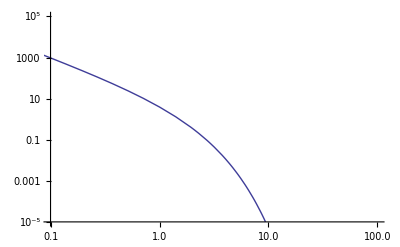

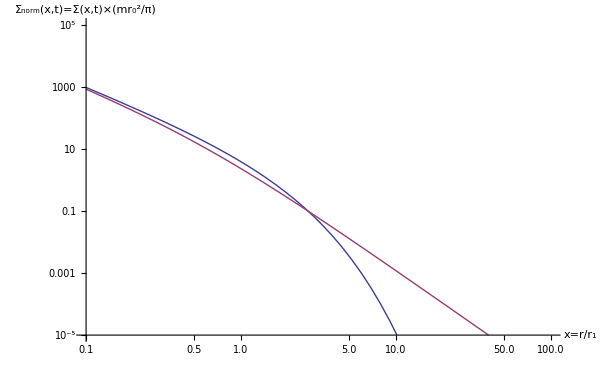

```mathematica
t1=0.004;
t2 = 0.008;
t3 = 0.016;
t4 = 0.032;
Const= 100;
ts = 1./(3.*x);
(*S1[x_,t1_]=(Const/(3*Pi*x^2))*(t1/ts+1.)^(-3/2)*Exp[-x/(t1/ts+1.)];*)
r=LogLogPlot[(Const/(3*Pi*x^2))*Exp[-x],{x,0.0001,1000},PlotRange->{{0.1,100},{10^-5,10^5}}]

g=LogLogPlot[
Evaluate[
Table[(Const/(3*Pi*x^2))*(t/ts+1.)^(-3/2)*Exp[-x/(t/ts+1.)],{t,{0.004,0.32}}]],{x,0.1,100},PlotRange->{{0.1,100},{10^-5,10^5}},AxesLabel->{Style["x=r/r_1",Italic,10],Style["Σ_norm(x,t)=Σ(x,t)×(mr_0^2/π)",Italic,10]}]
```